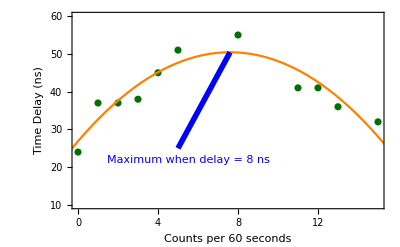

```mathematica
delays = {0,1,2,3,4,5,8,11,12,13,15};
counts = {24,37,37,38,45,51,55,41,41,36,32};
zipped = MapThread[List,{delays,counts}];
model=a x^2+b x+c;
nlm = NonlinearModelFit[zipped,model,{a,b,c},x];
max = Solve[D[nlm[x],x]==0,x]//Flatten;
arrow = Graphics[{Thickness[0.01],Blue,Arrow[{{5,25},{x/.max,nlm[x/.max]}}]}];
text = Graphics[{Blue,Style[Text["Maximum when delay = 8 ns",{5.5,22}],15]}];
plot1 = ListPlot[zipped,PlotLegends->Placed[{"Data"},{Right,Top}], PlotStyle->Directive[Darker[Darker[Green]]]];
plot2 = Plot[nlm[x],{x,-1,16},PlotLegends->Placed[{"Fit"},{Right,Top}], PlotStyle->Directive[Orange]];
finalplot=Show[plot1,plot2,arrow,text, Frame->True,PlotRange->{{0,15},{10,60}}, FrameLabel->{{"Time Delay (ns)",""},{"Counts per 60 seconds","S_1 vs S_3"}}]
Export[NotebookDirectory[]<>"Plots/DelayCalibration.svg",finalplot,"SVG"];
Export[NotebookDirectory[]<>"Plots/DelayCalibration.png",finalplot,"PNG"];
```